1.1.1

```mathematica
A=RandomInteger[{-10,10},{3,3}];
A=LowerTriangularize[A];
b=RandomInteger[{-10,10},{3}];
Print["A = ",MatrixForm[A]];
Print["b = ",MatrixForm[b]];
Print["x = ",MatrixForm[Inverse[A].b]];
```

A = (1 | 0 | 0
5 | -8 | 0
-2 | -6 | -1)

b = (8
8
8)

x = (8
4
-48)

1.1.2

```mathematica
A=RandomInteger[{-10,10},{3,3}];
A=UpperTriangularize[A];
b=RandomInteger[{-10,10},{3}];
Print["A = ",MatrixForm[A]];
Print["b = ",MatrixForm[b]];
Print["x = ",MatrixForm[Inverse[A].b]];
```

A = (9 | -8 | 2
0 | -4 | 10
0 | 0 | 3)

b = (2
-8
6)

x = (6
7
2)

1.1.3 (1.2.1, 1.2.2)

```mathematica
A=RandomInteger[{-10,10},{3,3}];
LU = First[LUDecomposition[A]];
Print["A = ",MatrixForm[A]];
Print["LU = ",MatrixForm[LU]];
```

LU = (-7 | 3 | -4
0 | -5 | -7
8/7 | -39/35 | -218/35)

A = (-8 | 9 | -3
-7 | 3 | -4
0 | -5 | -7)

1.3.1

```mathematica
P=RandomInteger[{-10,10},{3,3}];
A=Transpose[P].P;
L=CholeskyDecomposition[A];
Print["A = ",MatrixForm[A]];
Print["P = ",MatrixForm[P]];
Print["L = ",MatrixForm[N[L]]];
Print["L^T = ",MatrixForm[N[Transpose[L]]]];
Print["L^T L = ", MatrixForm[Transpose[L].L]]
```

A = (86 | -79 | 16
-79 | 146 | 21
16 | 21 | 21)

P = (-1 | 9 | 4
-9 | 8 | -2
2 | 1 | 1)

L = (9.27362 | -8.51879 | 1.72532
0. | 8.56914 | 4.16584
0. | 0. | 0.81795)

L^T = (9.27362 | 0. | 0.
-8.51879 | 8.56914 | 0.
1.72532 | 4.16584 | 0.81795)

L^T L = (86 | -79 | 16
-79 | 146 | 21
16 | 21 | 21)

```mathematica
A = HilbertMatrix[40];
L=CholeskyDecomposition[A];
MatrixForm[Transpose[N[L]]]
N[Part[L,14,14]]
```

(1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.5 | 0.288675 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.333333 | 0.288675 | 0.0745356 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.25 | 0.259808 | 0.111803 | 0.0188982 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.2 | 0.23094 | 0.127775 | 0.0377964 | 0.0047619 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.166667 | 0.206197 | 0.133099 | 0.0524951 | 0.0119048 | 0.00119647 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.142857 | 0.185577 | 0.133099 | 0.0629941 | 0.0194805 | 0.00358942 | 0.000300162 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.125 | 0.168394 | 0.130437 | 0.0701525 | 0.0265152 | 0.00676468 | 0.00105057 | 0.0000752328 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.111111 | 0.15396 | 0.126485 | 0.0748293 | 0.032634 | 0.0103081 | 0.00224121 | 0.000300931 | 0.000018845 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.1 | 0.141713 | 0.121967 | 0.0777074 | 0.0377622 | 0.0139159 | 0.00378205 | 0.000716924 | 0.0000848027 | 4.71855×10^-6 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.0909091 | 0.131216 | 0.117276 | 0.0792932 | 0.041958 | 0.0173949 | 0.00556183 | 0.00132764 | 0.000223165 | 0.0000235927 | 1.18111×10^-6 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.0833333 | 0.122132 | 0.112622 | 0.079954 | 0.0453297 | 0.0206351 | 0.00747758 | 0.00211374 | 0.000450049 | 0.0000679695 | 6.49613×10^-6 | 2.95584×10^-7 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.0769231 | 0.114201 | 0.108118 | 0.079954 | 0.0479961 | 0.023583 | 0.00944536 | 0.00304378 | 0.000771513 | 0.000148297 | 0.0000203357 | 1.7735×10^-6 | 7.39602×10^-8 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.0714286 | 0.107222 | 0.103817 | 0.0794837 | 0.05007 | 0.0262206 | 0.0114019 | 0.00408253 | 0.00118532 | 0.000272415 | 0.0000477324 | 5.99444×10^-6 | 4.80741×10^-7 | 1.85037×10^-8 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.0666667 | 0.101036 | 0.0997462 | 0.0786808 | 0.0516512 | 0.0285513 | 0.0133022 | 0.00519595 | 0.0016835 | 0.000444945 | 0.0000935555 | 0.000015063 | 1.74491×10^-6 | 1.29526×10^-7 | 4.62889×10^-9 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.0625 | 0.0955175 | 0.0959098 | 0.0776456 | 0.0528251 | 0.0305906 | 0.0151162 | 0.00635375 | 0.00225469 | 0.000667418 | 0.000161923 | 0.0000313812 | 4.67388×10^-6 | 5.02472×10^-7 | 3.47167×10^-8 | 1.15787×10^-9 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.0588235 | 0.0905647 | 0.0923041 | 0.076451 | 0.0536636 | 0.0323604 | 0.0168249 | 0.00753037 | 0.00288601 | 0.000938786 | 0.000255878 | 0.0000573827 | 0.0000103148 | 1.42926×10^-6 | 1.43346×10^-7 | 9.26293×10^-9 | 2.89608×10^-10 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.0555556 | 0.0860961 | 0.0889197 | 0.0751508 | 0.0542265 | 0.0338846 | 0.0184182 | 0.0087051 | 0.00356434 | 0.00125606 | 0.00037729 | 0.0000953081 | 0.0000198731 | 3.33109×10^-6 | 4.31532×10^-7 | 4.05604×10^-8 | 2.46167×10^-9 | 7.24333×10^-11 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.0526316 | 0.0820445 | 0.085744 | 0.0737845 | 0.0545633 | 0.0351878 | 0.0198917 | 0.00986173 | 0.00427721 | 0.00161493 | 0.000526905 | 0.000147047 | 0.0000346177 | 6.74545×10^-6 | 1.05921×10^-6 | 1.28839×10^-7 | 1.1394×10^-8 | 6.519×10^-10 | 1.81153×10^-11 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.05 | 0.0783547 | 0.0827636 | 0.0723809 | 0.0547149 | 0.0362937 | 0.0212452 | 0.0109879 | 0.00501322 | 0.00201032 | 0.000704492 | 0.000214048 | 0.0000557901 | 0.0000122985 | 2.24927×10^-6 | 3.3222×10^-7 | 3.80855×10^-8 | 3.18021×10^-9 | 1.72096×10^-10 | 4.5304×10^-12 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.047619 | 0.0749806 | 0.0799648 | 0.0709617 | 0.0547149 | 0.0372243 | 0.0224817 | 0.0120746 | 0.00576233 | 0.00243675 | 0.000909021 | 0.000297289 | 0.0000845304 | 0.0000206698 | 4.28433×10^-6 | 7.38267×10^-7 | 1.02934×10^-7 | 1.11586×10^-8 | 8.82541×10^-10 | 4.5304×10^-11 | 1.13295×10^-12 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.0454545 | 0.0718835 | 0.0773344 | 0.0695425 | 0.0545911 | 0.0379998 | 0.0236058 | 0.0131155 | 0.00651586 | 0.00288872 | 0.00113886 | 0.000397286 | 0.000121823 | 0.0000325549 | 7.49758×10^-6 | 1.46656×10^-6 | 2.38915×10^-7 | 3.15446×10^-8 | 3.24334×10^-9 | 2.43647×10^-10 | 1.1896×10^-11 | 2.83319×10^-13 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.0434783 | 0.069031 | 0.0748597 | 0.0681347 | 0.0543664 | 0.0386385 | 0.0246233 | 0.0141065 | 0.00726654 | 0.00336092 | 0.00139194 | 0.000514135 | 0.000168464 | 0.0000486314 | 0.0000122596 | 2.66847×10^-6 | 4.94166×10^-7 | 7.6338×10^-8 | 9.57181×10^-9 | 9.35914×10^-10 | 6.69497×10^-11 | 3.11651×10^-12 | 7.0848×10^-14 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.0416667 | 0.0663953 | 0.0725289 | 0.0667468 | 0.0540598 | 0.0391566 | 0.0255406 | 0.015045 | 0.00800833 | 0.00384832 | 0.00166592 | 0.000647565 | 0.000225044 | 0.0000695298 | 0.0000189629 | 4.52443×10^-6 | 9.3362×10^-7 | 1.64158×10^-7 | 2.41118×10^-8 | 2.87848×10^-9 | 2.68306×10^-10 | 1.83181×10^-11 | 8.14752×10^-13 | 1.77162×10^-14 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.04 | 0.0639526 | 0.070331 | 0.0653846 | 0.053687 | 0.0395688 | 0.0263645 | 0.01593 | 0.00873636 | 0.00434634 | 0.0019583 | 0.000797003 | 0.000291949 | 0.0000958114 | 0.0000280067 | 7.23909×10^-6 | 1.63953×10^-6 | 3.21615×10^-7 | 5.38311×10^-8 | 7.53638×10^-9 | 8.58579×10^-10 | 7.64583×10^-11 | 4.99252×10^-12 | 2.12594×10^-13 | 4.43001×10^-15 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.0384615 | 0.0616827 | 0.068256 | 0.0640523 | 0.0532609 | 0.0398879 | 0.0271017 | 0.0167614 | 0.00944676 | 0.00485083 | 0.00226655 | 0.000961635 | 0.000369369 | 0.000127953 | 0.0000397823 | 0.0000110352 | 2.71086×10^-6 | 5.8433×10^-7 | 1.09235×10^-7 | 1.74453×10^-8 | 2.33309×10^-9 | 2.54183×10^-10 | 2.16689×10^-11 | 1.35583×10^-12 | 5.53751×10^-14 | 1.10772×10^-15 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.037037 | 0.0595679 | 0.0662947 | 0.0627527 | 0.0527923 | 0.0401253 | 0.0277587 | 0.0175398 | 0.0101365 | 0.0053581 | 0.00258816 | 0.00114046 | 0.000457314 | 0.000166339 | 0.0000546602 | 0.0000161467 | 4.26172×10^-6 | 9.97493×10^-7 | 2.05119×10^-7 | 3.66244×10^-8 | 5.59281×10^-9 | 7.15949×10^-10 | 7.47357×10^-11 | 6.11028×10^-12 | 3.66996×10^-13 | 1.44004×10^-14 | 2.76982×10^-16 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.0357143 | 0.0575928 | 0.0644384 | 0.0614875 | 0.0522902 | 0.0402911 | 0.0283419 | 0.0182664 | 0.0108034 | 0.00586495 | 0.0029207 | 0.00133237 | 0.000555637 | 0.000211257 | 0.0000729804 | 0.000022812 | 6.419×10^-6 | 1.61594×10^-6 | 3.61188×10^-7 | 7.10084×10^-8 | 1.21344×10^-8 | 1.77526×10^-9 | 2.17929×10^-10 | 2.18353×10^-11 | 1.715×10^-12 | 9.90368×10^-14 | 3.73926×10^-15 | 6.92574×10^-17 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.0344828 | 0.0557442 | 0.0626795 | 0.0602578 | 0.0517621 | 0.0403942 | 0.0288572 | 0.018943 | 0.0114458 | 0.00636859 | 0.00326186 | 0.00153614 | 0.000664054 | 0.000262897 | 0.0000950442 | 0.0000312668 | 9.31944×10^-6 | 2.50375×10^-6 | 6.02493×10^-7 | 1.28867×10^-7 | 2.42688×10^-8 | 3.97659×10^-9 | 5.58355×10^-10 | 6.58417×10^-11 | 6.34226×10^-12 | 4.79289×10^-13 | 2.66507×10^-14 | 9.69604×10^-16 | 1.73171×10^-17 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.0333333 | 0.0540102 | 0.061011 | 0.0590639 | 0.051214 | 0.0404423 | 0.0293103 | 0.0195713 | 0.0120625 | 0.00686665 | 0.0036095 | 0.00175054 | 0.00078217 | 0.000321361 | 0.000121109 | 0.0000417386 | 0.0000131064 | 3.73342×10^-6 | 9.59652×10^-7 | 2.21178×10^-7 | 4.53557×10^-8 | 8.19684×10^-9 | 1.29005×10^-9 | 1.74128×10^-10 | 1.9755×10^-11 | 1.83219×10^-12 | 1.33412×10^-13 | 7.15295×10^-15 | 2.51098×10^-16 | 4.32992×10^-18 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.0322581 | 0.0523806 | 0.0594263 | 0.0579058 | 0.0506512 | 0.0404423 | 0.0297063 | 0.0201535 | 0.012653 | 0.00735712 | 0.00396165 | 0.00197429 | 0.000909499 | 0.000386664 | 0.000151387 | 0.0000544417 | 0.0000179267 | 5.38474×10^-6 | 1.46886×10^-6 | 3.61928×10^-7 | 8.00394×10^-8 | 1.57631×10^-8 | 2.7383×10^-9 | 4.14592×10^-10 | 5.38772×10^-11 | 5.88919×10^-12 | 5.26627×10^-13 | 3.6998×10^-14 | 1.91516×10^-15 | 6.49488×10^-17 | 1.08263×10^-18 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.03125 | 0.0508462 | 0.0579195 | 0.0567831 | 0.050078 | 0.0404002 | 0.0300503 | 0.0206918 | 0.0132169 | 0.00783835 | 0.00431649 | 0.00220616 | 0.00104549 | 0.000458746 | 0.000186039 | 0.0000695724 | 0.0000239272 | 7.54335×10^-6 | 2.17165×10^-6 | 5.68321×10^-7 | 1.34472×10^-7 | 2.85819×10^-8 | 5.41463×10^-9 | 9.05506×10^-10 | 1.32082×10^-10 | 1.65483×10^-11 | 1.74513×10^-12 | 1.50657×10^-13 | 1.02248×10^-14 | 5.11605×10^-16 | 1.67808×10^-17 | 2.70693×10^-19 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.030303 | 0.049399 | 0.0564853 | 0.0556953 | 0.0494979 | 0.0403215 | 0.0303467 | 0.0211884 | 0.0137541 | 0.00830898 | 0.0046724 | 0.00244492 | 0.00118953 | 0.000537478 | 0.000225182 | 0.0000873066 | 0.0000312519 | 0.0000102992 | 3.11452×10^-6 | 8.60889×10^-7 | 2.16508×10^-7 | 4.92724×10^-8 | 1.00811×10^-8 | 1.83976×10^-9 | 2.96604×10^-10 | 4.17375×10^-11 | 5.04807×10^-12 | 5.14243×10^-13 | 4.29106×10^-14 | 2.81658×10^-15 | 1.36377×10^-16 | 4.33109×10^-18 | 6.76815×10^-20 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.0294118 | 0.0480317 | 0.0551188 | 0.0546416 | 0.048914 | 0.0402107 | 0.0305996 | 0.0216456 | 0.014265 | 0.0087679 | 0.00502791 | 0.00268941 | 0.001341 | 0.000622675 | 0.000268885 | 0.000107797 | 0.0000400392 | 0.0000137449 | 4.34835×10^-6 | 1.26349×10^-6 | 3.35865×10^-7 | 8.12995×10^-8 | 1.78219×10^-8 | 3.51491×10^-9 | 6.18778×10^-10 | 9.62969×10^-11 | 1.30889×10^-11 | 1.53008×10^-12 | 1.50741×10^-13 | 1.21716×10^-14 | 7.73514×10^-16 | 3.62812×10^-17 | 1.11674×10^-18 | 1.69223×10^-20 | 0. | 0. | 0. | 0. | 0. | 0.
0.0285714 | 0.0467379 | 0.0538153 | 0.0536211 | 0.0483287 | 0.0400721 | 0.0308128 | 0.0220655 | 0.0147499 | 0.00921427 | 0.00538172 | 0.00293852 | 0.00149922 | 0.000714099 | 0.000317175 | 0.000131172 | 0.0000504197 | 0.0000179741 | 5.9277×10^-6 | 1.8032×10^-6 | 5.04234×10^-7 | 1.29096×10^-7 | 3.012×10^-8 | 6.3687×10^-9 | 1.21239×10^-9 | 2.06147×10^-10 | 3.10057×10^-11 | 4.07553×10^-12 | 4.60996×10^-13 | 4.39701×10^-14 | 3.43916×10^-15 | 2.11823×10^-16 | 9.63401×10^-18 | 2.87679×10^-19 | 4.23104×10^-21 | 0. | 0. | 0. | 0. | 0.
0.0277778 | 0.0455118 | 0.0525707 | 0.0526329 | 0.0477441 | 0.0399092 | 0.0309899 | 0.0224504 | 0.0152092 | 0.00964742 | 0.0057327 | 0.00319121 | 0.00166354 | 0.000811476 | 0.000370037 | 0.000157535 | 0.0000625143 | 0.0000230799 | 7.91006×10^-6 | 2.51014×10^-6 | 7.35341×10^-7 | 1.98174×10^-7 | 4.8935×10^-8 | 1.10193×10^-8 | 2.25026×10^-9 | 4.13983×10^-10 | 6.80681×10^-11 | 9.90579×10^-12 | 1.26054×10^-12 | 1.38111×10^-13 | 1.27666×10^-14 | 9.68223×10^-16 | 5.78513×10^-17 | 2.55368×10^-18 | 7.40431×10^-20 | 1.05787×10^-21 | 0. | 0. | 0. | 0.
0.027027 | 0.0443484 | 0.0513814 | 0.051676 | 0.0471619 | 0.0397253 | 0.031134 | 0.0228023 | 0.0156438 | 0.0100669 | 0.00607986 | 0.00344651 | 0.00183328 | 0.000914498 | 0.000427423 | 0.000186964 | 0.0000764326 | 0.0000291536 | 0.000010355 | 3.41716×10^-6 | 1.04496×10^-6 | 2.95212×10^-7 | 7.67794×10^-8 | 1.8309×10^-8 | 3.98407×10^-9 | 7.86689×10^-10 | 1.40026×10^-10 | 2.2288×10^-11 | 3.14164×10^-12 | 3.87429×10^-13 | 4.11579×10^-14 | 3.69064×10^-15 | 2.71649×10^-16 | 1.57598×10^-17 | 6.75774×10^-19 | 1.90416×10^-20 | 2.64492×10^-22 | 0. | 0. | 0.
0.0263158 | 0.0432428 | 0.0502436 | 0.0507492 | 0.0465834 | 0.0395232 | 0.0312481 | 0.0231232 | 0.0160542 | 0.0104723 | 0.00642232 | 0.00370351 | 0.00200781 | 0.00102283 | 0.000489249 | 0.000219515 | 0.0000922718 | 0.0000362829 | 0.0000133233 | 4.55954×10^-6 | 1.45086×10^-6 | 4.28119×10^-7 | 1.1679×10^-7 | 2.93501×10^-8 | 6.76698×10^-9 | 1.42457×10^-9 | 2.72295×10^-10 | 4.6942×10^-11 | 7.24059×10^-12 | 9.89533×10^-13 | 1.18372×10^-13 | 1.22041×10^-14 | 1.06254×10^-15 | 7.5969×10^-17 | 4.28303×10^-18 | 1.78548×10^-19 | 4.89311×10^-21 | 6.61291×10^-23 | 0. | 0.
0.025641 | 0.042191 | 0.0491543 | 0.0498516 | 0.0460099 | 0.0393054 | 0.031335 | 0.0234151 | 0.0164414 | 0.0108635 | 0.00675935 | 0.00396139 | 0.00218649 | 0.00113613 | 0.000555405 | 0.000255217 | 0.000110116 | 0.0000445515 | 0.0000168762 | 5.97458×10^-6 | 1.97273×10^-6 | 6.06083×10^-7 | 1.72792×10^-7 | 4.55716×10^-8 | 1.10788×10^-8 | 2.47246×10^-9 | 5.04094×10^-10 | 9.33668×10^-11 | 1.56051×10^-11 | 2.33478×10^-12 | 3.09655×10^-13 | 3.59646×10^-14 | 3.60165×10^-15 | 3.0472×10^-16 | 2.11805×10^-17 | 1.16136×10^-18 | 4.71043×10^-20 | 1.25645×10^-21 | 1.65337×10^-23 | 0.
0.025 | 0.041189 | 0.0481105 | 0.0489821 | 0.0454422 | 0.0390742 | 0.0313969 | 0.0236797 | 0.016806 | 0.0112404 | 0.00709032 | 0.00421938 | 0.00236869 | 0.00125403 | 0.000625757 | 0.000294079 | 0.000130036 | 0.0000540373 | 0.0000210744 | 7.70113×10^-6 | 2.63204×10^-6 | 8.39573×10^-7 | 2.49351×10^-7 | 6.87642×10^-8 | 1.7553×10^-8 | 4.13254×10^-9 | 8.93621×10^-10 | 1.7663×10^-10 | 3.17317×10^-11 | 5.14667×10^-12 | 7.47596×10^-13 | 9.63067×10^-14 | 1.08693×10^-14 | 1.05817×10^-15 | 8.70689×10^-17 | 5.88812×10^-18 | 3.14235×10^-19 | 1.24095×10^-20 | 3.22407×10^-22 | 4.13377×10^-24)

1.85037×10^-8

```mathematica
A ={{1,4.9176,1,3.472,0.998,1,7,4,42,3,1,0},{1,5.0208,1,3.531,1.5,2,7,4,62,1,1,0},{1,4.5429,1,2.275,1.175,1,6,3,40,2,1,0},{1,4.5573,1,4.05,1.232,1,6,3,54,4,1,0},{1,5.0597,1,4.455,1.121,1,6,3,42,3,1,0},{1,3.891,1,4.455,0.988,1,6,3,56,2,1,0},{1,5.898,1,5.85,1.24,1,7,3,51,2,1,1},{1,5.6039,1,9.52,1.501,0,6,3,32,1,1,0},{1,15.4202,2.5,9.8,3.42,2,10,5,42,2,1,1},{1,14.4598,2.5,12.8,3,2,9,5,14,4,1,1},{1,5.8282,1,6.435,1.225,2,6,3,32,1,1,0},{1,5.3003,1,4.9883,1.552,1,6,3,30,1,2,0},{1,6.2712,1,5.52,0.975,1,5,2,30,1,2,0},{1,5.9592,1,6.666,1.121,2,6,3,32,2,1,0},{1,5.05,1,5,1.02,0,5,2,46,4,1,1},{1,5.6039,1,9.52,1.501,0,6,3,32,1,1,0},{1,8.2464,1.5,5.15,1.664,2,8,4,50,4,1,0},{1,6.6969,1.5,6.092,1.488,1.5,7,3,22,1,1,1},{1,7.7841,1.5,7.102,1.376,1,6,3,17,2,1,0},{1,9.0384,1,7.8,1.5,1.5,7,3,23,3,3,0},{1,5.9894,1,5.52,1.256,2,6,3,40,4,1,1},{1,7.5422,1.5,4,1.69,1,6,3,22,1,1,0},{1,8.7951,1.5,9.89,1.82,2,8,4,50,1,1,1},{1,6.0931,1.5,6.7265,1.652,1,6,3,44,4,1,0},{1,8.3607,1.5,9.15,1.777,2.,8,4,48,1,1,1},{1,8.14,1,8,1.504,2,7,3,3,1,3,0},{1,9.1416,1.5,7.3262,1.831,1.5,8,4,31,4,1,0},{1,12,1.5,5,1.2,2,6,3,30,3,1,1}};
Dimensions[A]
```

{28,12}

```mathematica
QR=QRDecomposition[A];
Q=QR[[1]]
R=QR[[2]]
Dimensions[Q]
Dimensions[R]
Transpose[Q].R
```

{{-0.188982,-0.188982,-0.188982,-0.188982,-0.188982,-0.188982,-0.188982,-0.188982,-0.188982,-0.188982,-0.188982,-0.188982,-0.188982,-0.188982,-0.188982,-0.188982,-0.188982,-0.188982,-0.188982,-0.188982,-0.188982,-0.188982,-0.188982,-0.188982,-0.188982,-0.188982,-0.188982,-0.188982},{-0.153444,-0.146464,-0.178789,-0.177815,-0.143832,-0.222883,-0.0871297,-0.107023,0.556952,0.49199,-0.091851,-0.127558,-0.0618865,-0.0829902,-0.144488,-0.107023,0.071716,-0.0330921,0.0404461,0.125287,-0.0809474,0.0240839,0.10883,-0.0739332,0.0794473,0.0645191,0.132267,0.325609},{-0.0243327,-0.0115478,-0.0707525,-0.0689686,-0.00672862,-0.151513,0.0971244,0.0606898,-0.160768,-0.279748,0.0884772,0.0230782,0.143358,0.104706,-0.0079303,0.0606898,-0.0911278,-0.283088,-0.1484,0.486174,0.108448,-0.178368,-0.0231519,-0.35789,-0.0769677,0.374875,0.0197743,0.373888},{-0.178281,-0.177382,-0.282503,-0.100881,-0.0844072,-0.0259449,0.0169645,0.40869,-0.122516,0.233712,0.0805524,-0.0416577,-0.0356046,0.0977296,-0.0279349,0.40869,-0.195395,-0.0211141,0.0282563,0.0601919,-0.021508,-0.278307,0.26409,0.0742712,0.209801,0.125679,-0.0166186,-0.398572},{-0.0733645,0.365161,0.142397,0.108686,-0.0126787,-0.119464,0.0188506,0.0781269,0.440336,-0.0627546,-0.021361,0.339689,-0.202331,-0.125047,-0.127296,0.0781269,-0.00474497,-0.1905,-0.3465,0.127947,0.047713,0.0787036,-0.0959649,-0.0706198,-0.0950523,0.130007,0.0316838,-0.439749},{0.0620466,-0.275948,0.0720215,0.0273049,0.0497763,-0.039334,0.0770955,0.324181,0.137679,-0.0250158,-0.302958,0.0658752,0.105223,-0.302685,0.390369,0.324181,-0.157205,-0.12109,0.107222,0.082063,-0.265823,0.18189,-0.239328,0.00227206,-0.252471,-0.168062,0.034239,0.106482},{-0.478831,0.0295428,-0.0141407,0.0294324,-0.0401852,-0.109285,-0.329691,0.00425584,-0.0211323,0.11105,0.231853,0.220323,0.226433,0.169081,0.0562603,0.00425584,-0.274671,-0.103608,0.0813061,-0.0894053,0.244211,0.256732,-0.160889,0.261935,-0.186579,0.0257246,-0.274132,0.130154},{0.426942,0.296502,-0.00273664,0.0126286,0.0611957,0.0088066,-0.292563,0.181774,-0.16061,0.277349,0.0434693,0.0278446,-0.206587,0.0670818,-0.216493,0.181774,-0.0748266,-0.466405,0.0667758,-0.152901,0.0379385,-0.0247872,-0.00411096,-0.0723895,-0.033424,-0.241198,0.0208286,0.238121},{0.261224,-0.17594,0.135889,-0.178076,0.0026239,-0.169458,-0.174713,-0.00752035,-0.219197,0.187632,0.0321588,0.155806,-0.0875388,0.0243636,-0.255556,-0.00752035,-0.0708263,0.315343,0.24368,0.0424088,-0.0942538,0.245394,-0.267543,-0.148353,-0.178556,0.432972,0.151677,-0.196121},{-0.0168281,0.220326,0.0597369,-0.279445,-0.109143,0.0967882,0.0537533,0.12397,0.157292,-0.258214,0.106507,0.0969941,0.208567,-0.0417659,-0.237151,0.12397,-0.203803,0.157198,0.0840196,-0.217115,-0.37104,0.2456,0.225654,-0.294472,0.222299,-0.0199702,-0.274386,0.140657},{0.1634,0.0902384,-0.115852,0.0289163,-0.0570571,0.273729,-0.246226,-0.175185,-0.105551,0.120678,-0.266433,0.234876,0.330391,-0.23087,-0.055067,-0.175185,0.0366353,-0.161809,0.0512005,0.344062,-0.27645,-0.105062,0.095953,0.283536,0.103054,0.162964,-0.244211,-0.104678},{-0.205972,-0.0506082,-0.0233506,0.0909891,0.0803392,0.0999164,-0.154368,0.0883485,0.0954759,-0.252037,0.203308,-0.235313,0.151014,0.224316,-0.314347,0.0883485,0.356894,-0.233065,0.162999,0.0761929,-0.397894,0.0645477,-0.105224,0.166438,-0.158291,-0.0340435,0.31299,-0.0976059}}

{{-5.2915,-38.0255,-6.70887,-34.0346,-7.99905,-7.08683,-35.3397,-17.3864,-192.195,-11.9059,-6.4254,-1.70084},{0.,14.7842,1.9111,8.05393,2.35654,1.76758,4.46435,2.39661,-25.9563,0.989216,0.190167,1.21717},{0.,0.,-1.04344,-0.466732,-0.994628,0.405064,-1.32149,-1.22381,-17.437,-0.70393,1.88853,-0.252194},{0.,0.,0.,9.7344,0.52167,-0.682026,0.624424,0.192145,-13.8864,-1.65321,0.294479,0.132922},{0.,0.,0.,0.,1.13516,0.0941507,1.95265,1.21251,13.034,-1.01711,0.653265,-0.504417},{0.,0.,0.,0.,0.,-2.78646,-1.59335,-1.09893,-10.1172,0.671157,-0.00090063,-0.192103},{0.,0.,0.,0.,0.,0.,-2.77288,-1.44842,-23.3793,-0.718141,0.319394,-0.260224},{0.,0.,0.,0.,0.,0.,0.,1.28847,8.67648,0.788577,-0.96694,-0.620198},{0.,0.,0.,0.,0.,0.,0.,0.,-55.5821,-1.16243,1.01903,-0.882964},{0.,0.,0.,0.,0.,0.,0.,0.,0.,-5.75057,-0.168608,0.0904486},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.57932,-0.630095},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-1.61736}}

{12,28}

{12,12}

{{1.,4.9176,1.,3.472,0.998,1.,7.,4.,42.,3.,1.,8.37306×10^-17},{1.,5.0208,1.,3.531,1.5,2.,7.,4.,62.,1.,1.,2.93246×10^-16},{1.,4.5429,1.,2.275,1.175,1.,6.,3.,40.,2.,1.,1.69063×10^-17},{1.,4.5573,1.,4.05,1.232,1.,6.,3.,54.,4.,1.,8.50892×10^-18},{1.,5.0597,1.,4.455,1.121,1.,6.,3.,42.,3.,1.,-1.70838×10^-16},{1.,3.891,1.,4.455,0.988,1.,6.,3.,56.,2.,1.,8.85255×10^-17},{1.,5.898,1.,5.85,1.24,1.,7.,3.,51.,2.,1.,1.},{1.,5.6039,1.,9.52,1.501,-1.63925×10^-16,6.,3.,32.,1.,1.,8.90781×10^-17},{1.,15.4202,2.5,9.8,3.42,2.,10.,5.,42.,2.,1.,1.},{1.,14.4598,2.5,12.8,3.,2.,9.,5.,14.,4.,1.,1.},{1.,5.8282,1.,6.435,1.225,2.,6.,3.,32.,1.,1.,1.60604×10^-17},{1.,5.3003,1.,4.9883,1.552,1.,6.,3.,30.,1.,2.,1.32253×10^-16},{1.,6.2712,1.,5.52,0.975,1.,5.,2.,30.,1.,2.,-7.99923×10^-17},{1.,5.9592,1.,6.666,1.121,2.,6.,3.,32.,2.,1.,6.54331×10^-17},{1.,5.05,1.,5.,1.02,1.42238×10^-16,5.,2.,46.,4.,1.,1.},{1.,5.6039,1.,9.52,1.501,-1.63925×10^-16,6.,3.,32.,1.,1.,-1.78382×10^-17},{1.,8.2464,1.5,5.15,1.664,2.,8.,4.,50.,4.,1.,1.04741×10^-16},{1.,6.6969,1.5,6.092,1.488,1.5,7.,3.,22.,1.,1.,1.},{1.,7.7841,1.5,7.102,1.376,1.,6.,3.,17.,2.,1.,-1.48776×10^-16},{1.,9.0384,1.,7.8,1.5,1.5,7.,3.,23.,3.,3.,6.08613×10^-17},{1.,5.9894,1.,5.52,1.256,2.,6.,3.,40.,4.,1.,1.},{1.,7.5422,1.5,4.,1.69,1.,6.,3.,22.,1.,1.,-1.90829×10^-16},{1.,8.7951,1.5,9.89,1.82,2.,8.,4.,50.,1.,1.,1.},{1.,6.0931,1.5,6.7265,1.652,1.,6.,3.,44.,4.,1.,-1.27816×10^-16},{1.,8.3607,1.5,9.15,1.777,2.,8.,4.,48.,1.,1.,1.},{1.,8.14,1.,8.,1.504,2.,7.,3.,3.,1.,3.,-2.94274×10^-17},{1.,9.1416,1.5,7.3262,1.831,1.5,8.,4.,31.,4.,1.,2.37018×10^-16},{1.,12.,1.5,5.,1.2,2.,6.,3.,30.,3.,1.,1.}}

```mathematica
Rexpand=ArrayPad[QR[[2]],{{0,16},{0}}]//MatrixForm
```

(-5.2915 | -38.0255 | -6.70887 | -34.0346 | -7.99905 | -7.08683 | -35.3397 | -17.3864 | -192.195 | -11.9059 | -6.4254 | -1.70084
0. | 14.7842 | 1.9111 | 8.05393 | 2.35654 | 1.76758 | 4.46435 | 2.39661 | -25.9563 | 0.989216 | 0.190167 | 1.21717
0. | 0. | -1.04344 | -0.466732 | -0.994628 | 0.405064 | -1.32149 | -1.22381 | -17.437 | -0.70393 | 1.88853 | -0.252194
0. | 0. | 0. | 9.7344 | 0.52167 | -0.682026 | 0.624424 | 0.192145 | -13.8864 | -1.65321 | 0.294479 | 0.132922
0. | 0. | 0. | 0. | 1.13516 | 0.0941507 | 1.95265 | 1.21251 | 13.034 | -1.01711 | 0.653265 | -0.504417
0. | 0. | 0. | 0. | 0. | -2.78646 | -1.59335 | -1.09893 | -10.1172 | 0.671157 | -0.00090063 | -0.192103
0. | 0. | 0. | 0. | 0. | 0. | -2.77288 | -1.44842 | -23.3793 | -0.718141 | 0.319394 | -0.260224
0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.28847 | 8.67648 | 0.788577 | -0.96694 | -0.620198
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -55.5821 | -1.16243 | 1.01903 | -0.882964
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -5.75057 | -0.168608 | 0.0904486
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.57932 | -0.630095
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.61736
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Q.Rexpand//TableForm
```

(-0.188982 | -0.188982 | -0.188982 | -0.188982 | -0.188982 | -0.188982 | -0.188982 | -0.188982 | -0.188982 | -0.188982 | -0.188982 | -0.188982 | -0.188982 | -0.188982 | -0.188982 | -0.188982 | -0.188982 | -0.188982 | -0.188982 | -0.188982 | -0.188982 | -0.188982 | -0.188982 | -0.188982 | -0.188982 | -0.188982 | -0.188982 | -0.188982
-0.153444 | -0.146464 | -0.178789 | -0.177815 | -0.143832 | -0.222883 | -0.0871297 | -0.107023 | 0.556952 | 0.49199 | -0.091851 | -0.127558 | -0.0618865 | -0.0829902 | -0.144488 | -0.107023 | 0.071716 | -0.0330921 | 0.0404461 | 0.125287 | -0.0809474 | 0.0240839 | 0.10883 | -0.0739332 | 0.0794473 | 0.0645191 | 0.132267 | 0.325609
-0.0243327 | -0.0115478 | -0.0707525 | -0.0689686 | -0.00672862 | -0.151513 | 0.0971244 | 0.0606898 | -0.160768 | -0.279748 | 0.0884772 | 0.0230782 | 0.143358 | 0.104706 | -0.0079303 | 0.0606898 | -0.0911278 | -0.283088 | -0.1484 | 0.486174 | 0.108448 | -0.178368 | -0.0231519 | -0.35789 | -0.0769677 | 0.374875 | 0.0197743 | 0.373888
-0.178281 | -0.177382 | -0.282503 | -0.100881 | -0.0844072 | -0.0259449 | 0.0169645 | 0.40869 | -0.122516 | 0.233712 | 0.0805524 | -0.0416577 | -0.0356046 | 0.0977296 | -0.0279349 | 0.40869 | -0.195395 | -0.0211141 | 0.0282563 | 0.0601919 | -0.021508 | -0.278307 | 0.26409 | 0.0742712 | 0.209801 | 0.125679 | -0.0166186 | -0.398572
-0.0733645 | 0.365161 | 0.142397 | 0.108686 | -0.0126787 | -0.119464 | 0.0188506 | 0.0781269 | 0.440336 | -0.0627546 | -0.021361 | 0.339689 | -0.202331 | -0.125047 | -0.127296 | 0.0781269 | -0.00474497 | -0.1905 | -0.3465 | 0.127947 | 0.047713 | 0.0787036 | -0.0959649 | -0.0706198 | -0.0950523 | 0.130007 | 0.0316838 | -0.439749
0.0620466 | -0.275948 | 0.0720215 | 0.0273049 | 0.0497763 | -0.039334 | 0.0770955 | 0.324181 | 0.137679 | -0.0250158 | -0.302958 | 0.0658752 | 0.105223 | -0.302685 | 0.390369 | 0.324181 | -0.157205 | -0.12109 | 0.107222 | 0.082063 | -0.265823 | 0.18189 | -0.239328 | 0.00227206 | -0.252471 | -0.168062 | 0.034239 | 0.106482
-0.478831 | 0.0295428 | -0.0141407 | 0.0294324 | -0.0401852 | -0.109285 | -0.329691 | 0.00425584 | -0.0211323 | 0.11105 | 0.231853 | 0.220323 | 0.226433 | 0.169081 | 0.0562603 | 0.00425584 | -0.274671 | -0.103608 | 0.0813061 | -0.0894053 | 0.244211 | 0.256732 | -0.160889 | 0.261935 | -0.186579 | 0.0257246 | -0.274132 | 0.130154
0.426942 | 0.296502 | -0.00273664 | 0.0126286 | 0.0611957 | 0.0088066 | -0.292563 | 0.181774 | -0.16061 | 0.277349 | 0.0434693 | 0.0278446 | -0.206587 | 0.0670818 | -0.216493 | 0.181774 | -0.0748266 | -0.466405 | 0.0667758 | -0.152901 | 0.0379385 | -0.0247872 | -0.00411096 | -0.0723895 | -0.033424 | -0.241198 | 0.0208286 | 0.238121
0.261224 | -0.17594 | 0.135889 | -0.178076 | 0.0026239 | -0.169458 | -0.174713 | -0.00752035 | -0.219197 | 0.187632 | 0.0321588 | 0.155806 | -0.0875388 | 0.0243636 | -0.255556 | -0.00752035 | -0.0708263 | 0.315343 | 0.24368 | 0.0424088 | -0.0942538 | 0.245394 | -0.267543 | -0.148353 | -0.178556 | 0.432972 | 0.151677 | -0.196121
-0.0168281 | 0.220326 | 0.0597369 | -0.279445 | -0.109143 | 0.0967882 | 0.0537533 | 0.12397 | 0.157292 | -0.258214 | 0.106507 | 0.0969941 | 0.208567 | -0.0417659 | -0.237151 | 0.12397 | -0.203803 | 0.157198 | 0.0840196 | -0.217115 | -0.37104 | 0.2456 | 0.225654 | -0.294472 | 0.222299 | -0.0199702 | -0.274386 | 0.140657
0.1634 | 0.0902384 | -0.115852 | 0.0289163 | -0.0570571 | 0.273729 | -0.246226 | -0.175185 | -0.105551 | 0.120678 | -0.266433 | 0.234876 | 0.330391 | -0.23087 | -0.055067 | -0.175185 | 0.0366353 | -0.161809 | 0.0512005 | 0.344062 | -0.27645 | -0.105062 | 0.095953 | 0.283536 | 0.103054 | 0.162964 | -0.244211 | -0.104678
-0.205972 | -0.0506082 | -0.0233506 | 0.0909891 | 0.0803392 | 0.0999164 | -0.154368 | 0.0883485 | 0.0954759 | -0.252037 | 0.203308 | -0.235313 | 0.151014 | 0.224316 | -0.314347 | 0.0883485 | 0.356894 | -0.233065 | 0.162999 | 0.0761929 | -0.397894 | 0.0645477 | -0.105224 | 0.166438 | -0.158291 | -0.0340435 | 0.31299 | -0.0976059).(-5.2915 | -38.0255 | -6.70887 | -34.0346 | -7.99905 | -7.08683 | -35.3397 | -17.3864 | -192.195 | -11.9059 | -6.4254 | -1.70084
0. | 14.7842 | 1.9111 | 8.05393 | 2.35654 | 1.76758 | 4.46435 | 2.39661 | -25.9563 | 0.989216 | 0.190167 | 1.21717
0. | 0. | -1.04344 | -0.466732 | -0.994628 | 0.405064 | -1.32149 | -1.22381 | -17.437 | -0.70393 | 1.88853 | -0.252194
0. | 0. | 0. | 9.7344 | 0.52167 | -0.682026 | 0.624424 | 0.192145 | -13.8864 | -1.65321 | 0.294479 | 0.132922
0. | 0. | 0. | 0. | 1.13516 | 0.0941507 | 1.95265 | 1.21251 | 13.034 | -1.01711 | 0.653265 | -0.504417
0. | 0. | 0. | 0. | 0. | -2.78646 | -1.59335 | -1.09893 | -10.1172 | 0.671157 | -0.00090063 | -0.192103
0. | 0. | 0. | 0. | 0. | 0. | -2.77288 | -1.44842 | -23.3793 | -0.718141 | 0.319394 | -0.260224
0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.28847 | 8.67648 | 0.788577 | -0.96694 | -0.620198
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -55.5821 | -1.16243 | 1.01903 | -0.882964
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -5.75057 | -0.168608 | 0.0904486
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.57932 | -0.630095
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.61736
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

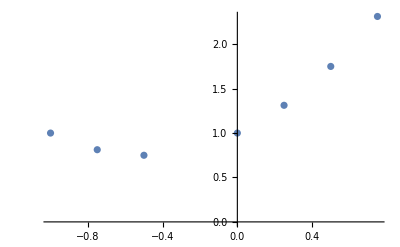

```mathematica
x={-1,-0.75,-0.5,0,0.25,0.5,0.75};
y={1,0.8125,0.75,1,1.3125,1.75,2.3125};
data={{-1,1},{-0.75,0.8125},{-0.5,0.75},{0,1},{0.25,1.3125},{0.5,1.75},{0.75,2.3125}};
ListPlot[data]
```

```mathematica
Fit[data,{1,c,c^2},c]
```

1.+1. c+1. c^2

```mathematica
Q={{-0.282409,-0.337601,0.131432,0.121446,-0.519144,-0.186974,-0.685403},{-0.429197,-0.194426,-0.54005,0.0507872,0.627729,0.00739144,-0.299427},{-0.132682,-0.470778,0.744853,0.0104434,0.437722,0.0935164,0.0741836}};
```

```mathematica
R={{1.3273,-0.741639,2.02479},{0,1.46201,0.51413},{0,0,1.62354}};
```

```mathematica
A={{1,-1,1},{0.5625,-0.75,1},{0.25,-0.5,1},{0,0,1},{0.0625,0.25,1},{0.25,0.5,1},{0.5625,0.75,1}};
```

```mathematica
QR=QRDecomposition[A];
Q=QR[[1]]
R=QR[[2]]
```

{{-0.753411,-0.423793,-0.188353,0.,-0.0470882,-0.188353,-0.423793},{-0.301805,-0.298013,-0.246449,0.,0.194884,0.437541,0.727972},{0.228101,-0.181778,-0.459077,-0.615937,-0.495497,-0.242477,0.143122}}

{{-1.3273,0.741639,-2.02479},{0.,1.46201,0.51413},{0.,0.,-1.62354}}

```mathematica
A={{1,4.9176,1,3.472,0.998,1,7,4,42,3,1,0},{1,5.0208,1,3.531,1.5,2,7,4,62,1,1,0},{1,4.5429,1,2.275,1.175,1,6,3,40,2,1,0},{1,4.5573,1,4.05,1.232,1,6,3,54,4,1,0},{1,5.0597,1,4.455,1.121,1,6,3,42,3,1,0},{1,3.891,1,4.455,0.988,1,6,3,56,2,1,0},{1,5.898,1,5.85,1.24,1,7,3,51,2,1,1},{1,5.6039,1,9.52,1.501,0,6,3,32,1,1,0},{1,15.4202,2.5,9.8,3.42,2,10,5,42,2,1,1},{1,14.4598,2.5,12.8,3,2,9,5,14,4,1,1},{1,5.8282,1,6.435,1.225,2,6,3,32,1,1,0},{1,5.3003,1,4.9883,1.552,1,6,3,30,1,2,0},{1,6.2712,1,5.52,0.975,1,5,2,30,1,2,0},{1,5.9592,1,6.666,1.121,2,6,3,32,2,1,0},{1,5.05,1,5,1.02,0,5,2,46,4,1,1},{1,5.6039,1,9.52,1.501,0,6,3,32,1,1,0},{1,8.2464,1.5,5.15,1.664,2,8,4,50,4,1,0},{1,6.6969,1.5,6.092,1.488,1.5,7,3,22,1,1,1},{1,7.7841,1.5,7.102,1.376,1,6,3,17,2,1,0},{1,9.0384,1,7.8,1.5,1.5,7,3,23,3,3,0},{1,5.9894,1,5.52,1.256,2,6,3,40,4,1,1},{1,7.5422,1.5,4,1.69,1,6,3,22,1,1,0},{1,8.7951,1.5,9.89,1.82,2,8,4,50,1,1,1},{1,6.0931,1.5,6.7265,1.652,1,6,3,44,4,1,0},{1,8.3607,1.5,9.15,1.777,2.,8,4,48,1,1,1},{1,8.14,1,8,1.504,2,7,3,3,1,3,0},{1,9.1416,1.5,7.3262,1.831,1.5,8,4,31,4,1,0},{1,12,1.5,5,1.2,2,6,3,30,3,1,1}};
y={25.9,29.5,27.9,25.9,29.9,29.9,30.9,28.9,84.9,82.9,35.9,31.5,31.0,30.9,30.0,28.9,36.9,41.9,40.5,43.9,37.5,37.9,44.5,37.9,38.9,36.9,45.8,41.0};
```

```mathematica
LeastSquares[A,y]
```

{2.07752,0.718888,9.6802,0.153506,13.6796,1.98683,-0.958225,-0.484023,-0.0736469,1.0187,1.44352,2.90279}